```mathematica
path = "C:\\Users\\enego\\OneDrive\\Documents\\GitHub\\durhack22\\ML\\mathematics_dataset-v1.0\\train-easy"
allFiles=FileNames["*.txt", path];
allData=AssociationMap[Import[#]<>Import[StringReplace[#,"train-easy"->"train-hard"]] <>Import[StringReplace[#,"train-easy"->"train-medium"]]&, allFiles];
```

C:\Users\enego\OneDrive\Documents\GitHub\durhack22\ML\mathematics_dataset-v1.0\train-easy

```mathematica
allData[[1]]
```

```mathematica
allData = KeyMap[StringDelete[StringDelete[StringDelete[#, path],".txt"],"\\"]&, allData];
```

```mathematica
largeQuestion = StringSplit[#, "\n"][[1;;;;2]]&/@ allData;
```

```mathematica
questions = RandomSample[#,16000]&/@ largeQuestion
```

```mathematica
naturalQuestions = StringRiffle[StringSplit[#]]&/@ StringReplace[#,{"-"-> " minus ", "+"-> "plus", "="-> "equals", "**"-> "to the power of", "."-> "", "*"-> " multiply ", "("-> "open bracket ", ")"-> " close bracket " }]&/@ questions
```

```mathematica
getAsso[key_] := Normal[AssociationThread[naturalQuestions[key],key&/@naturalQuestions[key]]]
```

```mathematica
plainData = Association[Flatten[getAsso[#]&/@Keys[naturalQuestions]]]
```

```mathematica
bert = NetModel["DistilBERT Trained on BookCorpus and English Wikipedia Data"]
```

NetChain[<>]

```mathematica
embedData = KeyMap[bert[#,TargetDevice->"GPU"]&,Association[RandomSample[Normal[plainData], 20000]]];
```

```mathematica
mixedData = RandomSample[Normal[embedData], Length[Normal[embedData]]];
Length[mixedData]
```

20000

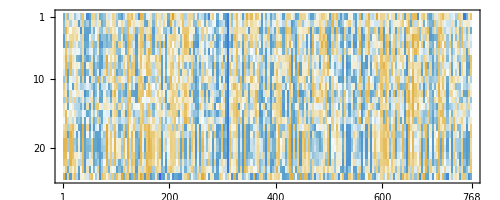

```mathematica
MatrixPlot[Keys[mixedData][[1]]]
```

```mathematica
{traingingData, vtData} = TakeDrop[mixedData,0.75*Length[mixedData]];
```

```mathematica
{testData, validationData} = TakeDrop[vtData, 0.8 * Length[vtData]];
```

```mathematica
Length[testData]
```

4000

```mathematica
network = NetChain[{DropoutLayer["Input"->{"Varying",768}],NetBidirectionalOperator[LongShortTermMemoryLayer[150]](*, GatedRecurrentLayer[50]*),(*NetMapOperator[LinearLayer[30]],*)LongShortTermMemoryLayer[56],AggregationLayer[Total,1], LinearLayer[56],SoftmaxLayer[ "Output" -> NetDecoder[{"Class",Keys[questions]}]] }]
```

NetChain[<>]

```mathematica
trainedNet = NetTrain[network,traingingData, ValidationSet->validationData, TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
NetMeasurements[trainedNet, testData, "ErrorRate"]
```

0.01175

```mathematica
Union[Values[Association[traingingData]]]
```

{algebra__linear_1d,algebra__linear_1d_composed,algebra__linear_2d,algebra__linear_2d_composed,algebra__polynomial_roots,algebra__polynomial_roots_composed,algebra__sequence_next_term,algebra__sequence_nth_term,arithmetic__add_or_sub,arithmetic__add_or_sub_in_base,arithmetic__add_sub_multiple,arithmetic__div,arithmetic__mixed,arithmetic__mul,arithmetic__mul_div_multiple,arithmetic__nearest_integer_root,arithmetic__simplify_surd,calculus__differentiate,calculus__differentiate_composed,comparison__closest,comparison__closest_composed,comparison__kth_biggest,comparison__kth_biggest_composed,comparison__pair,comparison__pair_composed,comparison__sort,comparison__sort_composed,measurement__conversion,measurement__time,numbers__base_conversion,numbers__div_remainder,numbers__div_remainder_composed,numbers__gcd,numbers__gcd_composed,numbers__is_factor,numbers__is_factor_composed,numbers__is_prime,numbers__is_prime_composed,numbers__lcm,numbers__lcm_composed,numbers__list_prime_factors,numbers__list_prime_factors_composed,numbers__place_value,numbers__place_value_composed,numbers__round_number,numbers__round_number_composed,polynomials__add,polynomials__coefficient_named,polynomials__collect,polynomials__compose,polynomials__evaluate,polynomials__evaluate_composed,polynomials__expand,polynomials__simplify_power,probability__swr_p_level_set,probability__swr_p_sequence}

```mathematica
trainedNet[bert["9 (a) A bag contains red counters and blue counters only. number of red counters: number of blue counters = 3 : 4. Write down the fraction of counters that are red.", TargetDevice->"GPU"], TargetDevice->"GPU"]
```

comparison__sort

```mathematica
TextRecognize[-Graphics-]
```

```mathematica
Expression[questions[[1]][[1]]]
```

Expression[Suppose -1382*k + 1464*k = 11972. Solve -32*w + 78 = -k for w.]

```mathematica
TextRecognize[]//AbsoluteTiming
```

{0.0004229,Suppose -1382«k + 1464«k = 11972. Solve -32«w + 78 = -k for w.}

```mathematica
ToString[ToExpression["n ^ 5"]]
```

5
n

```mathematica
ToString["4n ^ 5", StandardForm, CharacterEncoding->"ASCII"]
```

\!\(\*RowBox[{"\"4n ^ 5\""}]\)